```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
acceptMan=Import["blackman.pdf"][[1]];
rejectMan=Import["redman.pdf"][[1]];
```

```mathematica
{1.7,f[1.7]+0.1}
```

{1.7,1.32327}

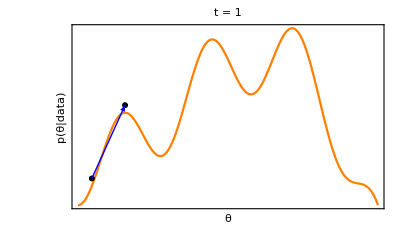

```mathematica
f[x_]:=Sin[x]^2+0.1x^2-0.01x^3
aXMax=FindRoot[f[x],{x,10}][[1,2]];
g1=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 1",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Blue,Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}]}],ListPlot[{{0.5,f[0.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{1.7,f[1.7]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black]]
```

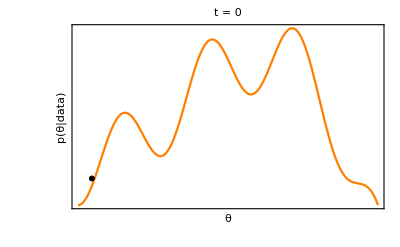

```mathematica
gStart=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 0",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange],ListPlot[{{0.5,f[0.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black]]
```

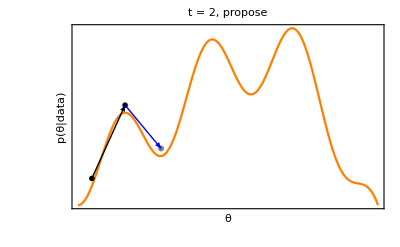

```mathematica
g2=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 2, propose",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{{Black,Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}]},{Blue,Arrow[{{1.7,f[1.7]+0.1},{3,f[3]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{3,f[3]+0.1}},PlotMarkers->acceptMan,PlotStyle->Gray]]
```

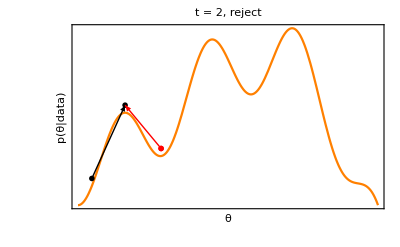

```mathematica
g3=Show[Plot[f[x],{x,0,aXMax},PlotLabel->"t = 2, reject",Frame->{True,True,False,False},FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}],{Red,Arrow[{{3,f[3]+0.1},{1.7,f[1.7]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{3,f[3]+0.1}},PlotMarkers->acceptMan,PlotStyle->Red]]
```

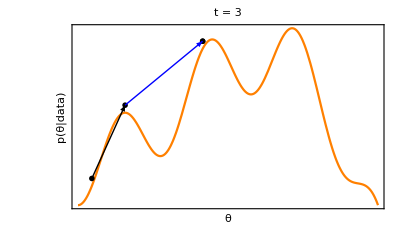

```mathematica
g4=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 3",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}],{Blue,Arrow[{{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{4.5,f[4.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black]]
```

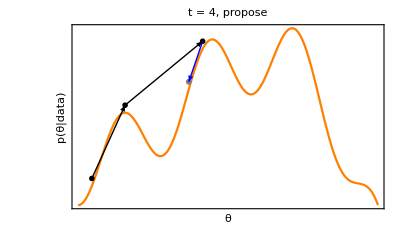

```mathematica
g5=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 4, propose",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}],{Black,Arrow[{{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}}]},{Blue,Arrow[{{4.5,f[4.5]+0.1},{4,f[4]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{4,f[4]+0.1}},PlotMarkers->acceptMan,PlotStyle->Gray]]
```

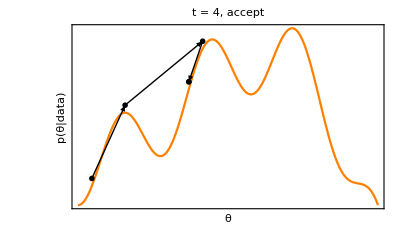

```mathematica
g6=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 4, accept",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}],{Black,Arrow[{{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}}]},{Black,Arrow[{{4.5,f[4.5]+0.1},{4,f[4]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{4,f[4]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black]]
```

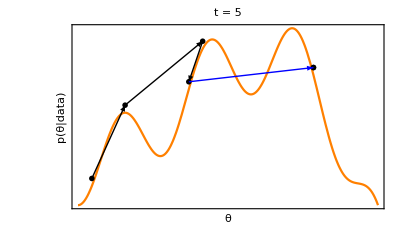

```mathematica
g7=Show[Plot[f[x],{x,0,aXMax},Frame->{True,True,False,False},PlotLabel->"t = 5",FrameTicks->{False,False,False,False},FrameLabel->{"θ","p(θ|data)"},PlotStyle->Orange,Epilog->{Arrow[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1}}],{Black,Arrow[{{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1}}]},{Black,Arrow[{{4.5,f[4.5]+0.1},{4,f[4]+0.1}}]},{Blue,Arrow[{{4,f[4]+0.1},{8.5,f[8.5]+0.1}}]}}],ListPlot[{{0.5,f[0.5]+0.1},{1.7,f[1.7]+0.1},{4.5,f[4.5]+0.1},{4,f[4]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black],ListPlot[{{8.5,f[8.5]+0.1}},PlotMarkers->acceptMan,PlotStyle->Black]]
```

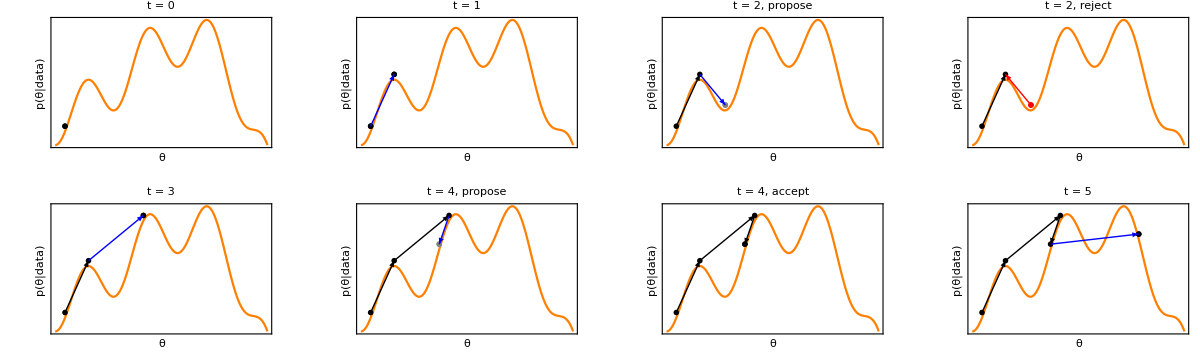

```mathematica
gFinal=Show[GraphicsGrid[{{gStart,g1,g2,g3},{g4,g5,g6,g7}}],ImageSize->1200]
```

```mathematica
Export["metropolisHastings_walker.pdf",gFinal]
```

metropolisHastings_walker.pdf